```mathematica
Clear["Global`*"]
```

```mathematica
Rep[line_]:=Flatten[Table[{line[[i]],line[[i]]+(line[[i+1]]-line[[i]])/3,(line[[i]]+line[[i+1]])/2+√3 Cross[(line[[i+1]]-line[[i]])/3]/2,line[[i+1]]-(line[[i+1]]-line[[i]])/3,line[[i+1]]},{i,1,Length[line]-1}],1]
```

```mathematica
l1={{0,0},{1/2,√3/2}};
l2={{1/2,√3/2},{1,0}};
l3={{1,0},{0,0}};
```

```mathematica
Snowflake[n_]:=Graphics[{Line[Nest[Rep,l1,n]],Line[Nest[Rep,l2,n]],Line[Nest[Rep,l3,n]]}]
```

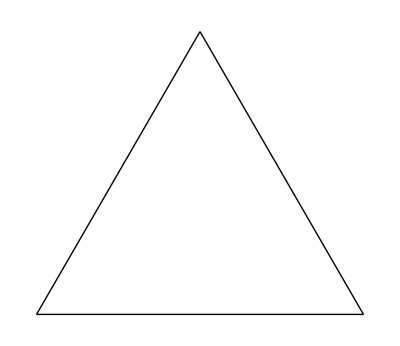

```mathematica
Snowflake[0]
```

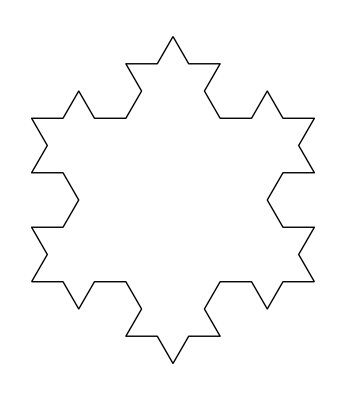

```mathematica
Snowflake[2]
```

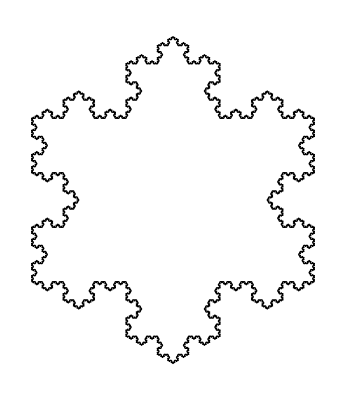

```mathematica
Snowflake[5]
```